## Initialization

```mathematica
$Assumptions=Join[{aa>0,β>0,κ>0,ϵ>0,lp>0,p0>0,μ0>0,θ0>0,μ>0,μ1>0,θx[x_]>0,μ2>0,θy[x_]>0,px[x_]>0,py[x_]>0,s1∈Integers,s1<3,s1>0,s2∈Integers,s2<3,s2>0,ϵ1>0,μ>0,α>0,lo>0,u[i_][t]>0,P0[t]>0,K0[t]∈ Reals,P0'[t]∈ Reals,K0'[t]∈ Reals,Λ>0,β>0,kx>0,-3 K0[t]^2+Λ P0[t]<0,t>0,Λ>0},Table[u[i][t]∈ Reals,{i,1,18}],Table[u[i]'[t]∈ Reals,{i,1,18}]];
```

```mathematica
filelocation=NotebookDirectory[];SetDirectory[filelocation];
```

```mathematica
(*H0=Import["H0.zip","H0.wl"];
```

```mathematica
ccdrule={CCD0->(μ^3 √P0[t] (-4 β^2 (Λ μ^2 P0[t]+3 Sin[β μ K0[t]]^4)+3 Sin[2 β μ K0[t]]^2))/(2 β^2 μ^2 κ)-λϕ (μ^3 (2 P0[t]^3 V1[Φ[t]]+2 P0[t]^3 V2[Φ[t]]+Π[t]^2))/(2 P0[t]^(3/2))};
```

```mathematica
transrule=Dispatch@(Join[Table[va[i][t]->P0[t]u[i][t],{i,1,9}],D[Table[va[i][t]->P0[t]u[i][t],{i,1,9}],t],Table[va[i][t]->K0[t]u[i][t],{i,10,18}],D[Table[va[i][t]->K0[t]u[i][t],{i,10,18}],t]]/.u->va);
```

```mathematica
transrule1=Dispatch@(Join[Table[va[i][t]->Sqrt[P0[t]]u[i][t]/K0[t],{i,10,18}],D[Table[va[i][t]->Sqrt[P0[t]]u[i][t]/K0[t],{i,10,18}],t],{va[19][t]->-P0[t]^(3/2)va[19][t],D[va[19][t]->-P0[t]^(3/2)va[19][t],t]}]/.u->va);
```

```mathematica
transrulebv={K0[t]->b0[t]Sqrt[P0[t]],K0'[t]->D[b0[t]Sqrt[P0[t]],t],μ->λ/Sqrt[P0[t]],P0[t]->v[t]^(2/3),P0'[t]->D[v[t]^(2/3),t]};
```

```mathematica
conformalt={ggg_'[t]->ggg'[η]/Sqrt[P0[η]],ggg_''[t]->D[ggg'[η]/Sqrt[P0[η]],η]/Sqrt[P0[η]]}
```

{ggg_'[t]→ggg'[η]/(√P0[η]),ggg_''[t]→(-(ggg'[η] P0'[η])/(2 P0[η]^(3/2))+ggg''[η]/(√P0[η]))/(√P0[η])}

```mathematica
physicalt={fff_'[η]->Sqrt[P0[t]]fff'[t],fff_''[η]->1/2 fff'[t] P0'[t]+P0[t] fff''[t]}
```

{fff_'[η]→√P0[t] fff'[t],fff_''[η]→1/2 fff'[t] P0'[t]+P0[t] fff''[t]}

```mathematica
Vlist[fff_]:=fff/.V1->V2/.V2->V/.V[Φ[t]]->1/4 V0[Φ[t]]/.V''[Φ[t]]->1/4V0''[Φ[t]]/.V'[Φ[t]]->1/4V0'[Φ[t]]
```

## Equation of Motion

```mathematica
Feom=Import["Feom.zip","Feom.wl"];
```

```mathematica
translp={V1[Φ[t]]->V1[Φ[t]]/λϕ^2,V1'[Φ[t]]->V1'[Φ[t]]/λϕ^2,V2'[Φ[t]]->V2'[Φ[t]]/λϕ^2,V1''[Φ[t]]->V1''[Φ[t]]/λϕ^2,V2[Φ[t]]->V2[Φ[t]]/λϕ^2,V2''[Φ[t]]->V2''[Φ[t]]/λϕ^2}
```

{V1[Φ[t]]→V1[Φ[t]]/λϕ^2,V1'[Φ[t]]→V1'[Φ[t]]/λϕ^2,V2'[Φ[t]]→V2'[Φ[t]]/λϕ^2,V1''[Φ[t]]→V1''[Φ[t]]/λϕ^2,V2[Φ[t]]→V2[Φ[t]]/λϕ^2,V2''[Φ[t]]→V2''[Φ[t]]/λϕ^2}

```mathematica
Feomn=Feom/.translp;
```

```mathematica
Feom=Feomn;
```

The 0th order equation of motion are then given by set ϵ_1 → 0. The continuum limit of the equation of motion is given by the limit where μ → 0, which gives the following equations

```mathematica
Feom0=DeleteCases[DeleteDuplicates[Thread[Flatten[Feom/.ϵ1->0]==0]/.lo->1//FullSimplify],True];
Feom0con=DeleteCases[DeleteDuplicates[Series[Feom0,{μ,0,2}]//Normal//Simplify],True];
Feom0//Vlist//FullSimplify
Feom0con//Vlist//FullSimplify
```

{2 (1-β^2+(1+β^2) Cos[2 β μ K0[t]]) P0[t]^2 Sin[β μ K0[t]]^2+β^2 κ λϕ λϕ1 μ^2 Π[t]^2+8 β^2 μ^2 P0[t]^(5/2) K0'[t]==(β^2 μ^2 P0[t]^3 (4 Λ λϕ+κ λϕ1 V0[Φ[t]]))/λϕ,(-β^2+(1+β^2) Cos[2 β μ K0[t]]) √P0[t] Sin[2 β μ K0[t]]==β μ P0'[t],λϕ λϕ1 Π[t]==P0[t]^(3/2) Φ'[t],(λϕ1 P0[t]^(3/2) V0'[Φ[t]])/λϕ+2 Π'[t]==0}

{4 K0[t]^2 P0[t]^2+κ λϕ λϕ1 Π[t]^2+8 P0[t]^(5/2) K0'[t]==(P0[t]^3 (4 Λ λϕ+κ λϕ1 V0[Φ[t]]))/λϕ,2 K0[t] √P0[t]==P0'[t],λϕ λϕ1 Π[t]==P0[t]^(3/2) Φ'[t],(λϕ1 P0[t]^(3/2) V0'[Φ[t]])/λϕ+2 Π'[t]==0}

The first order equations of motion are given by 
(d u^i)/dt=H0_ij u^j  
Thus here we will derive H0_ij as a 20-by-20 matrix.

```mathematica
Mdxy=Table[D[Feom[[i]],dtva[j]]//Simplify,{i,1,20},{j,1,20}];
IMd=Inverse[Mdxy]//Simplify;
Mxy=Table[D[Feom[[i]],va[j]]//Refine,{i,1,20},{j,1,20}];
H0S=IMd.Mxy;
```

Hc defines the continuum limit of H0

```mathematica
Hc=ParallelTable[Simplify[Normal@Series[H0S[[i,j]]/.CCD0->μ^3 P0[t]^(3/2)ρdust[t],{μ,0,0}]],{i,1,20},{j,1,20}];
```

Later on, we will use the notation where V^(1,...,9)= P_0 u^(1,...,9) , V^(10,...,18)= K_0 u^(10,...,18)

Define the rescaled matrix to simplify the expression (V_i → √P_0 V_i/K_0 =√P_0 u_i  for i=10,...,18, V_19 → (√P_0)^3 V_19 ).

```mathematica
eom=Table[(va[i]'[t]-∑_(j=1)^20 H0ccd[[i,j]]va[j][t])//Expand,{i,1,20}]/.transrule;
```

```mathematica
eomp=eom/.transrule1;
```

```mathematica
left1=Transpose[Table[D[eomp,va[i]'[t]],{i,1,20}]];
right1=Transpose[Table[D[eomp,va[i][t]],{i,1,20}]];
```

```mathematica
left1.Table[va[i]'[t],{i,1,20}]+right1.Table[va[i][t],{i,1,20}]-eomp//Expand
```

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

```mathematica
newH0=Inverse[left1].right1;
```

Transform it into minimum scheme.

```mathematica
newH0newscheme=(newH0/.CCD0-> μ^3*ρdust[t]*P0[t]^(3/2))/.K0[t]->b0[t]Sqrt[P0[t]]/.K0'[t]->D[b0[t]Sqrt[P0[t]],t]/.μ->λ/Sqrt[P0[t]]/.P0[t]->v[t]^(2/3)/.P0'[t]->D[v[t]^(2/3),t];
```

Simplification can be evaluated

```mathematica
(* newH0novnewschemefsimp=ParallelMap[Simplify,Flatten[newH0newscheme]]; *)
```

## SCPT variables & Closure condition

Import scalar constraint and vector constraint from data

```mathematica
Import["constraint.zip", "*"];
```

```mathematica
ScalarH=ScalarHo1+λϕ ScalarHs/.ϵ1->ϵ/.lo->1/.translp;
Diff=λϕ Diffs+Diffg/.ϵ1->ϵ/.translp;
Hphys=-ScalarH/.va[i_]->va[i][t]/.transrule;
Nshiftd=-Series[Diff/ScalarH,{ϵ,0,1}]/.va[i_]->va[i][t]/.transrule//Normal;
```

Define metric and their relation with V

```mathematica
qqu={{-u[1]+u[2]+u[3],-u[4]-u[7],-u[5]-u[8]},{-u[4]-u[7],u[1]-u[2]+u[3],-u[6]-u[9]},{-u[5]-u[8],-u[6]-u[9],u[1]+u[2]-u[3]}}/.u[i_]->va[i][t];
```

```mathematica
qqu//MatrixForm
```

(-va[1][t]+va[2][t]+va[3][t] | -va[4][t]-va[7][t] | -va[5][t]-va[8][t]
-va[4][t]-va[7][t] | va[1][t]-va[2][t]+va[3][t] | -va[6][t]-va[9][t]
-va[5][t]-va[8][t] | -va[6][t]-va[9][t] | va[1][t]+va[2][t]-va[3][t])

```mathematica
sv={1/(4 P0[t]) (Tr[qqu]-1/(-kx^2) (-kx^2) qqu[[1,1]]),-1/((4 P0[t]) (-kx^2)) (Tr[qqu]-3/(-kx^2) (-kx^2) qqu[[1,1]]),Table[1/(P0[t] (-kx^2)) (I kx qqu[[i,1]]-1/(-kx^2) (I kx)^3 qqu[[1,1]] KroneckerDelta[i,1]),{i,1,3}]}/.Table[va[i][t]->P0[t] va[i][t],{i,1,9}]//Simplify
```

{1/2 va[1][t],-(-2 va[1][t]+va[2][t]+va[3][t])/(2 kx^2),{0,(ⅈ (va[4][t]+va[7][t]))/kx,(ⅈ (va[5][t]+va[8][t]))/kx}}

```mathematica
(I kx Table[qqu[[i,1]],{i,1,3}]/.u[i_]->u[i][t])-Table[2 ((I kx) sv[[1]] KroneckerDelta[j,1]+(I kx)^3 sv[[2]] KroneckerDelta[j,1]+1/2 (I kx)^2 (sv[[3]][[j]]+sv[[3]][[1]] KroneckerDelta[1,j])),{j,1,3}]//FullSimplify
```

{0,0,0}

```mathematica
tmodemetric=Table[(qqu[[j,k]]/.u[i_]->u[i][t])-2 (sv[[1]] KroneckerDelta[j,k]+(I kx)^2 sv[[2]] KroneckerDelta[j,1] KroneckerDelta[1,k]+1/2 I kx (sv[[3]][[j]] KroneckerDelta[1,k]+sv[[3]][[k]] KroneckerDelta[1,j])),{j,1,3},{k,1,3}]//Simplify
```

{{0,0,0},{0,-va[2][t]+va[3][t],-va[6][t]-va[9][t]},{0,-va[6][t]-va[9][t],va[2][t]-va[3][t]}}

Define B, S_i and their continuum limit

```mathematica
bbd=-I kx Nshiftd[[1]]/kx^2/Sqrt[P0[t]];
```

```mathematica
ssd=Table[(Nshiftd[[i]]/Sqrt[P0[t]])-I kx bbd KroneckerDelta[i,1],{i,1,3}];
```

```mathematica
ssdjk=1/2 Table[ssd[[j]] (I kx) KroneckerDelta[k,1]+ssd[[k]] (I kx) KroneckerDelta[j,1],{j,1,3},{k,1,3}];
```

```mathematica
Nshift=Series[Nshiftd,{μ,0,0}]//Normal;
```

```mathematica
bbb=Series[bbd,{μ,0,0}]//Normal;sss=Series[ssd,{μ,0,0}]//Normal;sssjk=Series[ssdjk,{μ,0,0}]//Normal;
```

```mathematica
Ψg=sv[[1]]+Derivative[1][P0][t]/(2 Sqrt[P0[t]]) (bbb-Sqrt[P0[t]] (D[sv[[2]],t]))//FullSimplify
```

1/2 (va[1][t]-(4 ϵ λϕ √P0[t] (2 K0[t] P0[t] (kx (va[11][t]+va[12][t])-ⅈ β K0[t] (β va[6][t]-β va[9][t]-va[15][t]+va[18][t]))+kx β κ λϕ Π[t] va[20][t]) P0'[t])/(kx β (2 P0[t]^2 (-6 λϕ K0[t]^2+P0[t] (2 Λ λϕ+κ (V1[Φ[t]]+V2[Φ[t]])))+κ λϕ^2 Π[t]^2))+(P0'[t] (-2 va[1]'[t]+va[2]'[t]+va[3]'[t]))/(2 kx^2))

```mathematica
Φg=Derivative[1][P0][t]/(2 Sqrt[P0[t]]) Sqrt[P0[t]] (D[sv[[2]],t])+Sqrt[P0[t]] D[Sqrt[P0[t]] (D[sv[[2]],t]),t]//FullSimplify
```

(P0'[t] (2 va[1]'[t]-va[2]'[t]-va[3]'[t])+P0[t] (2 va[1]''[t]-va[2]''[t]-va[3]''[t]))/(2 kx^2)

```mathematica
rhodust=Series[Hphys/μ^3/P0[t]^(3/2)/.ϵ->0,{μ,0,0}]//Vlist//Normal//FullSimplify
```

-(2 Λ)/κ+(6 K0[t]^2)/(κ P0[t])-V0[Φ[t]]/(2 λϕ)-(λϕ Π[t]^2)/(2 P0[t]^3)

```mathematica
Λtrans=Solve[rhodust==ρdust[t],Λ]/.beq0//FullSimplify//Flatten
```

{Λ→(3 P0'[t]^2)/(4 P0[t]^2)-(κ (V0[Φ[t]]+2 λϕ ρdust[t]+Φ'[t]^2))/(4 λϕ)}

```mathematica
rhodustdt=ρdust'[t]->D[rhodust,t]/.beq0/.Solve[rhodust==ρdust[t],Λ]/.beq0//Vlist//FullSimplify
```

{ρdust'[t]→-(3 ρdust[t] P0'[t])/(2 P0[t])}

### Closure condition

```mathematica
clo=Get["clo1.wl"]/.ky->0/.kz->0/.transrule//Normal//Simplify;
```

```mathematica
Series[clo/μ^3/.kx->k,{μ,0,0}]//Normal//FullSimplify
```

{(2 ϵ1 P0[t] (ⅈ k va[1][t]+K0[t] (β va[6][t]-β va[9][t]-va[15][t]+va[18][t])))/(aa^2 β),(2 ϵ1 P0[t] (ⅈ k va[4][t]+K0[t] (-β va[5][t]+β va[8][t]+va[14][t]-va[17][t])))/(aa^2 β),(2 ϵ1 P0[t] (ⅈ k va[5][t]+K0[t] (β va[4][t]-β va[7][t]-va[13][t]+va[16][t])))/(aa^2 β)}

```mathematica
gaussc={1/(2 β)(ⅈ kx va[5][t]+β K0[t] (va[4][t]-va[7][t])+P0[t] (-va[13][t]+va[16][t])),-1/(2 β)(ⅈ kx va[4][t]+β K0[t] (-va[5][t]+va[8][t])+P0[t] (va[14][t]-va[17][t])),1/(2 β)(ⅈ kx va[1][t]+β K0[t] (va[6][t]-va[9][t])+P0[t] (-va[15][t]+va[18][t]))}/.transrule//FullSimplify
```

{(P0[t] (ⅈ kx va[5][t]+K0[t] (β va[4][t]-β va[7][t]-va[13][t]+va[16][t])))/(2 β),(P0[t] (-ⅈ kx va[4][t]+K0[t] (β va[5][t]-β va[8][t]-va[14][t]+va[17][t])))/(2 β),(P0[t] (ⅈ kx va[1][t]+K0[t] (β va[6][t]-β va[9][t]-va[15][t]+va[18][t])))/(2 β)}

## Continuum limit

### Second order eom

```mathematica
eomconu=Table[(va[i]'[t]+∑_(j=1)^20 Hc[[i,j]]va[j][t])//Expand,{i,1,20}]/.transrule/.λϕ1->1/.lo->1;
```

```mathematica
backeomgr0={4 K0[t]^2 P0[t]^2+κ λϕ Π[t]^2+8 P0[t]^(5/2) K0'[t]==2 P0[t]^3 (2 Λ+κ λϕ (V1[Φ[t]]+V2[Φ[t]])),2 K0[t] √P0[t]==P0'[t]}/.translp
```

{4 K0[t]^2 P0[t]^2+κ λϕ Π[t]^2+8 P0[t]^(5/2) K0'[t]==2 P0[t]^3 (2 Λ+κ λϕ (V1[Φ[t]]/λϕ^2+V2[Φ[t]]/λϕ^2)),2 K0[t] √P0[t]==P0'[t]}

```mathematica
backeoms={-λϕ Π[t]+P0[t]^(3/2) Φ'[t]==0,-λϕ P0[t]^(3/2) (V1'[Φ[t]]+V2'[Φ[t]])==Π'[t]}/.translp
```

{-λϕ Π[t]+P0[t]^(3/2) Φ'[t]==0,-λϕ P0[t]^(3/2) (V1'[Φ[t]]/λϕ^2+V2'[Φ[t]]/λϕ^2)==Π'[t]}

```mathematica
beq0=Flatten@Join[D[P0'[t]->2 K0[t] √P0[t],t]/.Solve[Join[backeomgr0,backeoms],{K0'[t],K0[t],Π[t],Π'[t]}]//FullSimplify,{Solve[Join[backeomgr0,backeoms],{K0'[t],K0[t],Π[t],Π'[t]}]}]//FullSimplify
```

{P0''[t]→(P0'[t]^2+(P0[t]^2 (4 Λ λϕ+2 κ (V1[Φ[t]]+V2[Φ[t]])-κ Φ'[t]^2))/λϕ)/(4 P0[t]),K0'[t]→(-λϕ P0'[t]^2+P0[t]^2 (4 Λ λϕ+2 κ (V1[Φ[t]]+V2[Φ[t]])-κ Φ'[t]^2))/(8 λϕ P0[t]^(3/2)),K0[t]→P0'[t]/(2 √P0[t]),Π[t]→(P0[t]^(3/2) Φ'[t])/λϕ,Π'[t]→-(P0[t]^(3/2) (V1'[Φ[t]]+V2'[Φ[t]]))/λϕ}

```mathematica
sol1=Solve[Table[((eomconu[[i]])//Simplify)==0,{i,1,9}],Table[va[i][t],{i,10,18}]];
```

```mathematica
sol0=Solve[Table[(eomconu[[i]]//Simplify)==0,{i,10,18}],Table[va[i]'[t],{i,10,18}]];
```

```mathematica
sols1=Solve[((eomconu[[20]])/.sol0/.sol1//Simplify)==0,va[19][t]];
sols0=Solve[((eomconu[[19]])/.sol0/.sol1/.sols1//Simplify)==0,va[19]'[t]];
```

```mathematica
eom2og=(Table[D[eomconu[[i]],t],{i,1,9}]/.sol0/.sol1/.sols1/.sols0/.beq0)[[1,1]];
```

```mathematica
eom2os=((D[eomconu[[20]],t])/.sol0/.sol1/.sols1/.sols0/.beq0)[[1,1]];
```

### Tensor mode

Tensor mode condition:

```mathematica
testini2={u[1][t]->0,u[2][t]->-u[3][t],u[4][t]->0,u[5][t]->0,u[7][t]->0,u[8][t]->0,u[20][t]->0}/.u->va;
```

```mathematica
tmodek=sol1/.testini2/.D[testini2,t]/.D[testini2,t,t]//FullSimplify;
```

and the non trivial metric is the tensor part

```mathematica
qqu/.testini2//MatrixForm
```

(0 | 0 | 0
0 | 2 va[3][t] | -va[6][t]-va[9][t]
0 | -va[6][t]-va[9][t] | -2 va[3][t])

Continuum limit of closure and solutions

```mathematica
Thread[Flatten[Normal@Series[clo,{μ,0,3}]/.tmodek/.testini2/.beq0]==0]//FullSimplify
solclot=Solve[%,{va[6]'[t]}][[1]]//FullSimplify
```

{(ρdust[t] (va[6]'[t]-va[9]'[t]))/(κ P0[t]^2 ρdust[t]-α β^2 P0'[t]^2)==0,True,True}

{va[6]'[t]→va[9]'[t]}

One can check the shift vector is 0

```mathematica
Nshift/.tmodek/.beq0/.testini2/.solclot//FullSimplify
```

{{0,0,0}}

```mathematica
eom2ot=DeleteCases[Flatten[eom2og/.testini2/.D[testini2,t]/.D[testini2,t,t]/.solclot/.D[solclot,t]/.D[solclot,t,t]//Simplify],0];
```

There are only 4 non trivial equations left:

```mathematica
Dimensions[eom2ot]
```

{4}

The scalar part of EoMs are automatically satisfied.

```mathematica
eom2os/.testini2/.D[testini2,t]/.D[testini2,t,t]/.solclot/.D[solclot,t]/.D[solclot,t,t]//Simplify
```

{{0}}

```mathematica
eom2ot//Vlist//FullSimplify//Expand
```

{-kx^2 va[3][t]-3/2 P0'[t] va[3]'[t]-P0[t] va[3]''[t],kx^2 va[3][t]+3/2 P0'[t] va[3]'[t]+P0[t] va[3]''[t],1/2 kx^2 va[6][t]+1/2 kx^2 va[9][t]+3/2 P0'[t] va[9]'[t]+P0[t] va[9]''[t],1/2 kx^2 va[6][t]+1/2 kx^2 va[9][t]+3/2 P0'[t] va[9]'[t]+P0[t] va[9]''[t]}

```mathematica
%/.conformalt/.t->η//FullSimplify
```

{-kx^2 va[3][η]-(P0'[η] va[3]'[η])/P0[η]-va[3]''[η],kx^2 va[3][η]+(P0'[η] va[3]'[η])/P0[η]+va[3]''[η],1/2 kx^2 (va[6][η]+va[9][η])+(P0'[η] va[9]'[η])/P0[η]+va[9]''[η],1/2 kx^2 (va[6][η]+va[9][η])+(P0'[η] va[9]'[η])/P0[η]+va[9]''[η]}

recall in metric form, h_23=u[6]+u[9],h_22=-u[2]+u[3] =2u[3]= -h_33

```mathematica
eom2ot/.va->u/.{u[9][t]->h[2,3][t]-u[6][t],u[9]'[t]->h[2,3]'[t]/2,u[3][t]->h[2,2][t]/2,u[9]''[t]->h[2,3]''[t]/2,u[3]''[t]->h[2,2]''[t]/2,u[3]'[t]->h[2,2]'[t]/2}//FullSimplify
```

{1/4 (-2 kx^2 h[2,2][t]-3 P0'[t] h[2,2]'[t]-2 P0[t] h[2,2]''[t]),1/4 (2 kx^2 h[2,2][t]+3 P0'[t] h[2,2]'[t]+2 P0[t] h[2,2]''[t]),1/4 (2 kx^2 h[2,3][t]+3 P0'[t] h[2,3]'[t]+2 P0[t] h[2,3]''[t]),1/4 (2 kx^2 h[2,3][t]+3 P0'[t] h[2,3]'[t]+2 P0[t] h[2,3]''[t])}

In conformal time

```mathematica
2*%/.conformalt/.t->η/.P0'[η]->ch[η]P0[η]*2//FullSimplify//Expand
```

{-kx^2 h[2,2][η]-2 ch[η] h[2,2]'[η]-h[2,2]''[η],kx^2 h[2,2][η]+2 ch[η] h[2,2]'[η]+h[2,2]''[η],kx^2 h[2,3][η]+2 ch[η] h[2,3]'[η]+h[2,3]''[η],kx^2 h[2,3][η]+2 ch[η] h[2,3]'[η]+h[2,3]''[η]}

### Scalar mode

```mathematica
testini3={u[6][t]->-u[9][t],u[2][t]->u[3][t],u[5][t]->0,u[8][t]->0,u[4][t]->0,u[7][t]->0}/.u->va
```

{va[6][t]→-va[9][t],va[2][t]→va[3][t],va[5][t]→0,va[8][t]→0,va[4][t]→0,va[7][t]→0}

```mathematica
smodek=sol1/.testini3/.D[testini3,t]/.D[testini3,t,t]//FullSimplify;
```

The vector part of the shift vector is 0

```mathematica
sss/.smodek/.testini3//FullSimplify
```

{{0,0,0}}

The metric reads

```mathematica
qqu/.u[i_]->u[i][t]/.testini3//MatrixForm
```

(-va[1][t]+2 va[3][t] | 0 | 0
0 | va[1][t] | 0
0 | 0 | va[1][t])

Solution of the closure:

```mathematica
Thread[Flatten[Normal@Series[clo,{μ,0,3}]/.smodek/.testini3/.beq0]==0]//FullSimplify
solclos=Solve[%,{va[9]'[t]}][[1]]
```

{(ⅈ kx α β P0'[t] (κ va[20][t] Φ'[t]+2 va[1]'[t])+2 κ P0[t]^(3/2) ρdust[t] va[9]'[t])/(κ P0[t]^2 ρdust[t]-α β^2 P0'[t]^2)==0,True,True}

{va[9]'[t]→-(ⅈ kx α β P0'[t] (κ va[20][t] Φ'[t]+2 va[1]'[t]))/(2 κ P0[t]^(3/2) ρdust[t])}

The equation of motion:

```mathematica
eom2sog=DeleteCases[Flatten[eom2og/.testini3/.D[testini3,t]/.D[testini3,t,t]/.solclos/.D[solclos,t]/.D[solclos,t,t]/.beq0//Expand//Simplify],0];
```

```mathematica
eom2sos=DeleteCases[Flatten[eom2os/.testini3/.D[testini3,t]/.D[testini3,t,t]/.solclos/.D[solclos,t]/.D[solclos,t,t]/.beq0//Expand//Simplify],0];
```

Transform to SCPT variables

```mathematica
sv2trans=Solve[sv[[2]]==ee[t]/.testini3,va[3][t]][[1]]
sv1trans1=Solve[sv[[1]]==ψ[t],va[1][t]][[1]]
```

{va[3][t]→-kx^2 ee[t]+va[1][t]}

{va[1][t]→2 ψ[t]}

Rewrite the first equation

```mathematica
eom2sog[[1]]/.beq0/.sv2trans/.D[sv2trans,t]/.D[sv2trans,t,t]/.sv1trans1/.D[sv1trans1,t]/.D[sv1trans1,t,t]//Vlist//FullSimplify;
%/.conformalt/.t->η//FullSimplify
Solve[%==0, ψ''[η]]/.P0'[η]->2P0[η]*Hubble[η]//FullSimplify//Expand
```

-(κ P0[η] va[20][η] V0'[Φ[η]])/(4 λϕ)+(2 P0'[η] ψ'[η])/P0[η]+(κ Φ'[η] va[20]'[η])/(2 λϕ)+2 ψ''[η]

{{ψ''[η]→(κ P0[η] va[20][η] V0'[Φ[η]])/(8 λϕ)-2 Hubble[η] ψ'[η]-(κ Φ'[η] va[20]'[η])/(4 λϕ)}}

Using the solution of first equation

```mathematica
sv1trans=Solve[Flatten[eom2sog][[1]]==0,va[1]''[t]][[1]];
sv1trans2=Solve[Flatten[eom2sog][[1]]==0/.sv2trans/.D[sv2trans,t]/.D[sv2trans,t,t]/.sv1trans1/.D[sv1trans1,t]/.D[sv1trans1,t,t],ψ''[t]][[1]];
```

The left 2 equations are equal

```mathematica
eom2sog[[2]]-eom2sog[[3]]/.beq0/.sv2trans/.D[sv2trans,t]/.D[sv2trans,t,t]/.sv1trans1/.D[sv1trans1,t]/.D[sv1trans1,t,t]//Vlist//FullSimplify
```

0

Transform to SCPT variables again

```mathematica
blist=Flatten[bb[t]->bbb/.ϵ->1/.testini3/.smodek/.solclos/.beq0/.sv1trans1/.D[sv1trans1,t]//Vlist//FullSimplify]
```

{bb[t]→-(4 λϕ P0[t]^(3/2) (κ va[20][t] Φ'[t]+4 ψ'[t]))/(-3 λϕ P0'[t]^2+P0[t]^2 (4 Λ λϕ+κ (V0[Φ[t]]+Φ'[t]^2)))}

```mathematica
btrans=Solve[bb[t]==(bb[t]/.blist),{ψ'[t]}][[1]]
```

{ψ'[t]→1/(16 λϕ P0[t]^(3/2))(-4 Λ λϕ bb[t] P0[t]^2-κ bb[t] P0[t]^2 V0[Φ[t]]+3 λϕ bb[t] P0'[t]^2-4 κ λϕ P0[t]^(3/2) va[20][t] Φ'[t]-κ bb[t] P0[t]^2 Φ'[t]^2)}

```mathematica
eom2sog[[2]]+eom2sog[[3]]/.sv1trans/.sv2trans/.D[sv2trans,t]/.D[sv2trans,t,t]/.sv1trans1/.D[sv1trans1,t]/.D[sv1trans1,t,t]/.sv1trans2/.btrans/.beq0/.Λtrans/.rhodustdt//Vlist;
Solve[%==0,ee''[t]]//Expand
Solve[%%==0/.conformalt/.t->η,ee''[η]]/.λϕ->1//Expand
```

{{ee''[t]→ψ[t]/P0[t]+(α bb[t] P0'[t])/(4 P0[t]^(3/2))-(3 ee'[t] P0'[t])/(2 P0[t])-(α va[20][t] V0'[Φ[t]])/(2 P0[t] ρdust[t])+(α va[20][t] V0'[Φ[t]])/(2 λϕ P0[t] ρdust[t])+(α Φ'[t] va[20]'[t])/(P0[t] ρdust[t])-(α Φ'[t] va[20]'[t])/(λϕ P0[t] ρdust[t])}}

{{ee''[η]→ψ[η]+(α bb[η] P0'[η])/(4 P0[η])-(ee'[η] P0'[η])/P0[η]}}

Now we are only left with scalar field equations. Define the perturbed dust density

```mathematica
rhodust1s=D[Series[Series[Hphys/μ^3/(1/2 (2 P0[t]^(3/2)+ϵ √P0[t] va[1][t]+ϵ √P0[t] va[2][t]+ϵ √P0[t] va[3][t])/.transrule)//Normal//Expand,{ϵ,0,1}] ,{μ,0,0}]//Normal,ϵ]/.sols1/.smodek/.testini3/.D[testini3,t]/.D[testini3,t,t]/.solclos/.D[solclos,t]/.D[solclos,t,t]/.btrans/.Λtrans/.beq0/.λϕ->1//Vlist//FullSimplify
```

{{-1/2 va[20][t] V0'[Φ[t]]+(2 kx^2 α P0'[t] (κ va[20][t] Φ'[t]+2 va[1]'[t]))/(κ^2 P0[t]^2 ρdust[t])+(2 kx^2 va[1][t]+P0'[t] (va[1]'[t]+2 va[3]'[t]))/(κ P0[t])-Φ'[t] va[20]'[t]}}

Define variable Q as Q=δΦ-(P_0 V_1 ∂_t Φ)/(∂_t P_0)

```mathematica
Qtrans=Solve[Q[t]== va[20][t]-Sqrt[P0[t]]Φ'[t]1/2va[1][t]/(P0'[t]/(2Sqrt[P0[t]])),{va[20][t]}][[1]]/.sv1trans1
```

{va[20][t]→(Q[t] P0'[t]+2 P0[t] ψ[t] Φ'[t])/P0'[t]}

```mathematica
beq02=Solve[D[backeoms[[1]],t]/.beq0,Φ''[t]][[1]]//Vlist
beq03=D[beq02,t]/.beq0/.beq02//Vlist//FullSimplify
beqp02=D[beq0[[1]],t]/.beq0/.beq02/.beq03//Vlist//Simplify
```

{Φ''[t]→(-P0[t] V0'[Φ[t]]-3 P0'[t] Φ'[t])/(2 P0[t])}

{Φ^(3)[t]→1/(8 λϕ P0[t]^2)(6 λϕ P0[t] P0'[t] V0'[Φ[t]]+27 λϕ P0'[t]^2 Φ'[t]+P0[t]^2 Φ'[t] (-3 κ V0[Φ[t]]+3 κ Φ'[t]^2-4 λϕ (3 Λ+V0''[Φ[t]])))}

P0^(3)[t]→1/8 (-P0'[t]^3/P0[t]^2+(4 κ P0[t] V0'[Φ[t]] Φ'[t])/λϕ+(3 P0'[t] (4 Λ λϕ+κ V0[Φ[t]]+κ Φ'[t]^2))/λϕ)

```mathematica
Qeom1=eom2sos[[1]]/.Solve[rhodust1s==ρdust1[t] ,va[3]'[t]][[1]]/.Qtrans/.D[Qtrans,t]/.D[Qtrans,t,t]/.sv2trans/.D[sv2trans,t]/.sv1trans1/.D[sv1trans1,t]/.D[sv1trans1,t,t]/.(sv1trans2/.Qtrans/.D[Qtrans,t]/.D[Qtrans,t,t])/.(btrans/.Λtrans/.(Qtrans/.sv1trans1))/.Λtrans/.beq0/.beq02/.beq03/.beqp02/.sv1trans/.Λtrans/.beq0/.λϕ->1//Vlist//FullSimplify
```

1/(4 P0[t] P0'[t]^3)(6 P0'[t]^4 Q'[t]-κ P0[t]^2 P0'[t]^2 (bb[t] √P0[t] ρdust[t] V0'[Φ[t]]-2 (ρdust1[t]-3 ρdust[t] ψ[t]) Φ'[t])+4 κ^2 P0[t]^4 ρdust[t] ψ[t] Φ'[t] (ρdust[t]+Φ'[t]^2)+κ P0[t]^3 ρdust[t] P0'[t] (-4 ψ[t] V0'[Φ[t]]+κ bb[t] √P0[t] Φ'[t] (ρdust[t]+Φ'[t]^2))+P0'[t]^3 (-3 κ bb[t] P0[t]^(3/2) ρdust[t] Φ'[t]+4 P0[t] Q''[t])+2 Q[t] P0'[t] (2 κ P0[t]^2 P0'[t] V0'[Φ[t]] Φ'[t]-κ^2 P0[t]^3 Φ'[t]^2 (ρdust[t]+Φ'[t]^2)+P0'[t]^2 (2 kx^2+P0[t] (3 κ Φ'[t]^2+V0''[Φ[t]]))))

```mathematica
D[Qeom1,#]&/@ {ψ[t],bb[t],ρdust1[t],Q[t],Q'[t],Q''[t]}//FullSimplify//Expand
%.{ψ[t],bb[t],ρdust1[t],Q[t],Q'[t],Q''[t]}-Qeom1//Expand
```

{-(κ P0[t]^2 ρdust[t] V0'[Φ[t]])/P0'[t]^2+(κ^2 P0[t]^3 ρdust[t]^2 Φ'[t])/P0'[t]^3-(3 κ P0[t] ρdust[t] Φ'[t])/(2 P0'[t])+(κ^2 P0[t]^3 ρdust[t] Φ'[t]^3)/P0'[t]^3,-(κ P0[t]^(3/2) ρdust[t] V0'[Φ[t]])/(4 P0'[t])-3/4 κ √P0[t] ρdust[t] Φ'[t]+(κ^2 P0[t]^(5/2) ρdust[t]^2 Φ'[t])/(4 P0'[t]^2)+(κ^2 P0[t]^(5/2) ρdust[t] Φ'[t]^3)/(4 P0'[t]^2),(κ P0[t] Φ'[t])/(2 P0'[t]),kx^2/P0[t]+(κ P0[t] V0'[Φ[t]] Φ'[t])/P0'[t]+3/2 κ Φ'[t]^2-(κ^2 P0[t]^2 ρdust[t] Φ'[t]^2)/(2 P0'[t]^2)-(κ^2 P0[t]^2 Φ'[t]^4)/(2 P0'[t]^2)+1/2 V0''[Φ[t]],(3 P0'[t])/(2 P0[t]),1}

0

```mathematica
D[P0[t]Qeom1/.conformalt/.η->t,#]&/@ {ψ[t],bb[t],ρdust1[t],Q[t],Q'[t],Q''[t]}//FullSimplify//Expand
1/4 %[[1]]*P0'[t]/P0[t]-%[[2]]//FullSimplify//Expand
```

{-(κ P0[t]^4 ρdust[t] V0'[Φ[t]])/P0'[t]^2+(κ^2 P0[t]^5 ρdust[t]^2 Φ'[t])/P0'[t]^3-(3 κ P0[t]^2 ρdust[t] Φ'[t])/(2 P0'[t])+(κ^2 P0[t]^4 ρdust[t] Φ'[t]^3)/P0'[t]^3,-(κ P0[t]^3 ρdust[t] V0'[Φ[t]])/(4 P0'[t])-3/4 κ P0[t] ρdust[t] Φ'[t]+(κ^2 P0[t]^4 ρdust[t]^2 Φ'[t])/(4 P0'[t]^2)+(κ^2 P0[t]^3 ρdust[t] Φ'[t]^3)/(4 P0'[t]^2),(κ P0[t]^2 Φ'[t])/(2 P0'[t]),kx^2+(κ P0[t]^2 V0'[Φ[t]] Φ'[t])/P0'[t]+3/2 κ Φ'[t]^2-(κ^2 P0[t]^3 ρdust[t] Φ'[t]^2)/(2 P0'[t]^2)-(κ^2 P0[t]^2 Φ'[t]^4)/(2 P0'[t]^2)+1/2 P0[t] V0''[Φ[t]],P0'[t]/P0[t],1}

3/8 κ P0[t] ρdust[t] Φ'[t]

### Vector mode

```mathematica
testini4={u[6][t]->0,u[9][t]->0,u[3][t]->0,u[2][t]->0,u[1][t]->0,u[4][t]->1/2 (g47[t]-h[1,2][t]),u[7][t]->1/2 (-g47[t]-h[1,2][t]),u[5][t]->1/2 (g58[t]-h[1,3][t]),u[8][t]->1/2 (-g58[t]-h[1,3][t]),u[20][t]->0}/.u->va;
```

```mathematica
vmodek=sol1/.testini4/.D[testini4,t]/.D[testini4,t,t]/.beq0//Simplify;
```

The scalar part of the shift vector is 0

```mathematica
bbb/.vmodek/.testini4//Simplify
```

{0}

The metric reads

```mathematica
qqu/.u[i_]->u[i][t]/.testini4//Simplify//MatrixForm
```

(0 | h[1,2][t] | h[1,3][t]
h[1,2][t] | 0 | 0
h[1,3][t] | 0 | 0)

```mathematica
Thread[Flatten[Normal@Series[clo,{μ,0,3}]/.vmodek/.testini4/.beq0]==0]//Simplify
solclov=Solve[%,{g47'[t],g58'[t]}][[1]];
```

{True,(κ^2 P0[t]^(7/2) ρdust[t]^2 g58'[t]-α β^2 κ P0[t]^(3/2) ρdust[t] g58'[t] P0'[t]^2+2 ⅈ kx^3 α^2 β P0[t] P0'[t] (g47'[t]-h[1,2]'[t])+ⅈ kx α β κ P0[t]^2 ρdust[t] P0'[t] (2 g47'[t]-h[1,2]'[t])+ⅈ kx α^2 β^3 P0'[t]^3 h[1,2]'[t]+kx^2 α κ P0[t]^(5/2) ρdust[t] (g58'[t]-h[1,3]'[t])-kx^2 α^2 β^2 √P0[t] P0'[t]^2 (g58'[t]+h[1,3]'[t]))/(κ^2 P0[t]^4 ρdust[t]^2-4 kx^2 α^2 β^2 P0[t] P0'[t]^2-2 α β^2 κ P0[t]^2 ρdust[t] P0'[t]^2+α^2 β^4 P0'[t]^4)==0,(-κ^2 P0[t]^(7/2) ρdust[t]^2 g47'[t]+α β^2 κ P0[t]^(3/2) ρdust[t] g47'[t] P0'[t]^2+kx^2 α κ P0[t]^(5/2) ρdust[t] (-g47'[t]+h[1,2]'[t])+kx^2 α^2 β^2 √P0[t] P0'[t]^2 (g47'[t]+h[1,2]'[t])+2 ⅈ kx^3 α^2 β P0[t] P0'[t] (g58'[t]-h[1,3]'[t])+ⅈ kx α β κ P0[t]^2 ρdust[t] P0'[t] (2 g58'[t]-h[1,3]'[t])+ⅈ kx α^2 β^3 P0'[t]^3 h[1,3]'[t])/(κ^2 P0[t]^4 ρdust[t]^2-4 kx^2 α^2 β^2 P0[t] P0'[t]^2-2 α β^2 κ P0[t]^2 ρdust[t] P0'[t]^2+α^2 β^4 P0'[t]^4)==0}

#### eom

```mathematica
eom2ov=DeleteCases[Flatten[eom2og/.testini4/.D[testini4,t]/.D[testini4,t,t]/.beq0/.solclov/.D[solclov,t]/.beq0],0];
```

```mathematica
Length[eom2ov]
```

4

```mathematica
eom2ov1={eom2ov[[1]]+eom2ov[[3]],eom2ov[[1]]-eom2ov[[3]],eom2ov[[2]]-eom2ov[[4]],eom2ov[[2]]+eom2ov[[4]]}/.rhodustdt//Simplify
```

{-((2 kx^2 α+3 κ P0[t] ρdust[t]) P0'[t] h[1,2]'[t])/(2 (kx^2 α+κ P0[t] ρdust[t]))-P0[t] h[1,2]''[t],(kx α (2 kx^3 α √P0[t] P0'[t] h[1,2]'[t]-2 ⅈ kx^2 α β P0'[t]^2 h[1,3]'[t]+2 kx κ P0[t]^(5/2) ρdust[t] h[1,2]''[t]+P0[t]^(3/2) (3 kx κ ρdust[t] P0'[t] h[1,2]'[t]+2 kx^3 α h[1,2]''[t])-2 ⅈ β κ P0[t]^2 ρdust[t] P0'[t] h[1,3]''[t]-ⅈ β P0[t] P0'[t] (3 κ ρdust[t] P0'[t] h[1,3]'[t]+2 kx^2 α h[1,3]''[t])))/(2 √P0[t] (kx^2 α+κ P0[t] ρdust[t])^2),(kx α (ⅈ β (2 kx^2 α+3 κ P0[t] ρdust[t]) P0'[t]^2 h[1,2]'[t]+P0'[t] (2 kx^3 α √P0[t] h[1,3]'[t]+3 kx κ P0[t]^(3/2) ρdust[t] h[1,3]'[t]+2 ⅈ kx^2 α β P0[t] h[1,2]''[t]+2 ⅈ β κ P0[t]^2 ρdust[t] h[1,2]''[t])+2 kx P0[t]^(3/2) (kx^2 α+κ P0[t] ρdust[t]) h[1,3]''[t]))/(2 √P0[t] (kx^2 α+κ P0[t] ρdust[t])^2),-((2 kx^2 α+3 κ P0[t] ρdust[t]) P0'[t] h[1,3]'[t])/(2 (kx^2 α+κ P0[t] ρdust[t]))-P0[t] h[1,3]''[t]}

Only two of them are independent

```mathematica
eom2ov2=eom2ov1[[{1,4}]]/.beq0//FullSimplify
```

{-((2 kx^2 α+3 κ P0[t] ρdust[t]) P0'[t] h[1,2]'[t])/(2 (kx^2 α+κ P0[t] ρdust[t]))-P0[t] h[1,2]''[t],-((2 kx^2 α+3 κ P0[t] ρdust[t]) P0'[t] h[1,3]'[t])/(2 (kx^2 α+κ P0[t] ρdust[t]))-P0[t] h[1,3]''[t]}

```mathematica
eom2ov1/.Solve[Thread[eom2ov2==0],{h[1,2]''[t],h[1,3]''[t]}][[1]]/.beq0//FullSimplify
```

{0,0,0,0}

Write it into SCPT form

```mathematica
(sss/.Flatten[vmodek]/.testini4/.D[testini4,t]/.D[testini4,t,t]/.lo->1/.beq0/.solclov/.D[solclov,t]/.beq0//Vlist)/.Λtrans/.ϵ->1//Simplify
```

{0,-(2 ⅈ kx √P0[t] h[1,2]'[t])/(kx^2 α+κ P0[t] ρdust[t]),-(2 ⅈ kx √P0[t] h[1,3]'[t])/(kx^2 α+κ P0[t] ρdust[t])}

```mathematica
sssjkv=(sssjk/.Flatten[vmodek]/.testini4/.D[testini4,t]/.D[testini4,t,t]/.lo->1/.beq0/.solclov/.D[solclov,t]/.beq0//Vlist)/.Λtrans/.conformalt/.t->η/.ϵ->1//Simplify
```

{{0,(kx^2 h[1,2]'[η])/(kx^2 α+κ P0[η] ρdust[η]),(kx^2 h[1,3]'[η])/(kx^2 α+κ P0[η] ρdust[η])},{(kx^2 h[1,2]'[η])/(kx^2 α+κ P0[η] ρdust[η]),0,0},{(kx^2 h[1,3]'[η])/(kx^2 α+κ P0[η] ρdust[η]),0,0}}

```mathematica
-eom2ov2[[1]]+α ch[η]sssjkv[[1,2]]/.conformalt/.t->η/.P0'[η]->2 ch[η] P0[η]//FullSimplify
```

2 ch[η] h[1,2]'[η]+h[1,2]''[η]

## Background solution

```mathematica
scalarpini = {V1[Φ[t]]->0,V2[Φ[t]]->(3 ms^2)/(2 κ)(1-Exp[-√(κ/3)Φ[t]])^2/λϕ^2}//FullSimplify;
```

```mathematica
scalarp=Join[scalarpini,D[scalarpini,Φ[t]],D[scalarpini,Φ[t],Φ[t]]];
```

```mathematica
(*backeom={(-Sin[2 β μ K0[t]]^2+4 β^2 (Λ μ^2 P0[t]+Sin[β μ K0[t]]^4-2 μ^2 √P0[t] K0'[t]))/(√P0[t])==0,√P0[t] (2 β^2 Sin[2 β μ K0[t]]-(1+β^2) Sin[4 β μ K0[t]])+2 β μ P0'[t]==0};
```

```mathematica
backeomgr={K0'[t]-(4 β^2 Λ μ^2 P0[t]+4 β^2 Sin[β μ K0[t]]^4-Sin[2 β μ K0[t]]^2)/(8 β^2 μ^2 √P0[t])-λϕ(κ (2 P0[t]^3 (V1[Φ[t]]+V2[Φ[t]])-Π[t]^2))/(8 P0[t]^(5/2))==0,P0'[t]+(√P0[t] (2 β^2 Sin[2 β μ K0[t]]-Sin[4 β μ K0[t]]-β^2 Sin[4 β μ K0[t]]))/(2 β μ)==0}//FullSimplify
```

{((P0[t]^2 (-4 β^2 Sin[β μ K0[t]]^4+Sin[2 β μ K0[t]]^2))/(β^2 μ^2)-2 P0[t]^3 (2 Λ+κ λϕ (V1[Φ[t]]+V2[Φ[t]]))+κ λϕ Π[t]^2)/(8 P0[t]^(5/2))+K0'[t]==0,(-β^2+(1+β^2) Cos[2 β μ K0[t]]) √P0[t] Sin[2 β μ K0[t]]==β μ P0'[t]}

```mathematica
backeoms={-λϕ Π[t]+P0[t]^(3/2) Φ'[t]==0,λϕ P0[t]^(3/2) (V1'[Φ[t]]+V2'[Φ[t]])==-Π'[t]}
```

{-λϕ Π[t]+P0[t]^(3/2) Φ'[t]==0,λϕ P0[t]^(3/2) (V1'[Φ[t]]+V2'[Φ[t]])==-Π'[t]}

```mathematica
backeom=Join[backeomgr,backeoms];
```

Transform to minimum scheme

```mathematica
backeombv=backeom//.transrulebv//FullSimplify;
```

This gives the initial value of the evaluation

```mathematica
varini={v[0]==1,b0[0]==1.21*10^(-06),Φ[0]==1.0672244842086127,Π[0]==-5.029282328194059*10^(-09)}
```

{v[0]==1,b0[0]==1.21×10^-6,Φ[0]==1.06722,Π[0]==-5.02928×10^-9}

This define the parameters where λ = √Δ.

```mathematica
paras={λ->10,β->1,κ->16π,Λ->0,λϕ->1,ms->2.43721050651927389913147144195892934703806531615555286407470703125*10^(-06)}
```

{λ→10,β→1,κ→16 π,Λ→0,λϕ→1,ms→2.4372105065192738991314714419589293470380653161555528640747070313×10^-6}

The evaluation of minimum scheme

```mathematica
sol=Module[{ct,stepc=0},Monitor[NDSolve[ReleaseHold[SetPrecision[Hold[Join[backeombv//Expand,varini]//.scalarp//.paras],50]]/.x_Real:>SetPrecision[ToExpression@ToString[x,InputForm],50],{b0[t],v[t],Π[t],Φ[t]},{t,-1.614*10^6,0},WorkingPrecision->30,MaxSteps->200000,Method->"ExplicitRungeKutta",AccuracyGoal->16,PrecisionGoal->16,StepMonitor:>{ct=t,stepc++}],{ct,stepc}]]
```

{{b0[t]→InterpolatingFunction[…][t],v[t]→InterpolatingFunction[…][t],Π[t]→InterpolatingFunction[…][t],Φ[t]→InterpolatingFunction[…][t]}}

```mathematica
solf=SetPrecision[sol,MachinePrecision][[1]];
```

The position of the bounce.

```mathematica
tb=FindRoot[v'[t]/.D[sol[[1,2]],t]/.t->t0,{t0,-1.6134*10^6}]
```

{t0→-1.61332×10^6}

Below is the evaluation of the continuum background EoMs

```mathematica
backeomc=Evaluate[Series[backeombv//Expand,{λ,0,1}]//Expand//Normal]//FullSimplify
```

{(-3 κ λϕ Π[t]^2+6 v[t]^2 (-2 b0[t]^2+κ λϕ (V1[Φ[t]]+V2[Φ[t]])+2 (Λ-2 b0'[t]))-8 b0[t] v[t] v'[t])/v[t]^(1/3)==0,(λ (3 b0[t] v[t]-v'[t]))/v[t]^(1/3)==0,λϕ Π[t]==v[t] Φ'[t],λϕ v[t] (V1'[Φ[t]]+V2'[Φ[t]])+Π'[t]==0}

```mathematica
solc=Monitor[NDSolve[ReleaseHold[SetPrecision[Hold[Join[backeomc,varini]//.scalarp//.paras],50]]/.x_Real:>SetPrecision[ToExpression@ToString[x,InputForm],50],{b0[t],v[t],Π[t],Φ[t]},{t,-3*10^7,3*10^7},WorkingPrecision->30,MaxSteps->200000,Method->"ImplicitRungeKutta",AccuracyGoal->23,PrecisionGoal->23,StepMonitor:>{c=t,d++}],{c,d}]
```

{{b0[t]→InterpolatingFunction[…][t],v[t]→InterpolatingFunction[…][t],Π[t]→InterpolatingFunction[…][t],Φ[t]→InterpolatingFunction[…][t]}}

Now we define the average scheme EoMs which depends on the solution of minimum scheme

```mathematica
backeomave=backeombv/.λ->λ0[t]/.λ0[t]->2 * λ*v[t]^(1/3)/(v[t]^(1/3)/.solf);
```

```mathematica
solave=Monitor[NDSolve[ReleaseHold[SetPrecision[Hold[Join[backeomave//Expand,varini]//.scalarp//.paras],50]]/.x_Real:>SetPrecision[ToExpression@ToString[x,InputForm],50],{b0[t],v[t],Π[t],Φ[t]},{t,-1.614*10^6,0},WorkingPrecision->30,MaxSteps->200000,Method->"ExplicitRungeKutta",AccuracyGoal->16,PrecisionGoal->16,StepMonitor:>{c=t,d++}],{c,d}]
```

InterpolatingFunction::dmval: Input value {1.00000000000000145821198401343×10^-15} lies outside the range of data in the interpolating function. Extrapolation will be used.

NDSolve::ndstf: At t == -1.61363838915129015743711066699×10^6, system appears to be stiff. Methods Automatic, BDF, or StiffnessSwitching may be more appropriate.

{{b0[t]→InterpolatingFunction[…][t],v[t]→InterpolatingFunction[…][t],Π[t]→InterpolatingFunction[…][t],Φ[t]→InterpolatingFunction[…][t]}}

The position of bounce in ave scheme

```mathematica
tbave=FindRoot[v'[t]/.D[solave[[1,2]],t]/.t->t0,{t0,-1.6130*10^6}]
```

InterpolatingFunction::dmval: Input value {-1.62541×10^6} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {-1.61424×10^6} lies outside the range of data in the interpolating function. Extrapolation will be used.

{t0→-1.61332×10^6}

```mathematica
rhodustmin=rhodust//.transrulebv//Expand
```

-(2 Λ)/κ-(6 Sin[β λ b0[t]]^4)/(κ λ^2)+(3 Sin[2 β λ b0[t]]^2)/(2 β^2 κ λ^2)-λϕ V1[Φ[t]]-λϕ V2[Φ[t]]-(λϕ Π[t]^2)/(2 v[t]^2)

```mathematica
rhodustave=rhodustmin/.λ->λ0[t]/.λ0[t]->2 * λ*v[t]^(1/3)/(v[t]^(1/3)/.solf);
```

```mathematica
rhodustc=Series[rhodustmin,{λ,0,0}]//Normal
```

-(2 Λ)/κ+(6 b0[t]^2)/κ-λϕ V1[Φ[t]]-λϕ V2[Φ[t]]-(λϕ Π[t]^2)/(2 v[t]^2)

```mathematica
rhophi=-(-(2 Λ)/κ-λϕ V1[Φ[t]]-λϕ V2[Φ[t]]-(λϕ Π[t]^2)/(2 v[t]^2))
```

(2 Λ)/κ+λϕ V1[Φ[t]]+λϕ V2[Φ[t]]+(λϕ Π[t]^2)/(2 v[t]^2)

```mathematica
rhototal=rhodustmin+rhophi//FullSimplify
```

(3 (-4 β^2 Sin[β λ b0[t]]^4+Sin[2 β λ b0[t]]^2))/(2 β^2 κ λ^2)

```mathematica
rhototalave=rhototal/.λ->λ0[t]/.λ0[t]->2 * λ*v[t]^(1/3)/(v[t]^(1/3)/.solf);
```

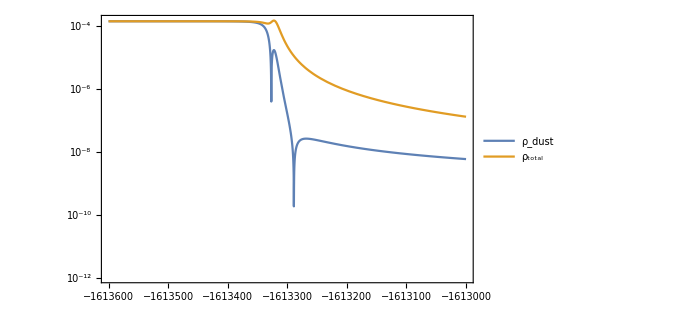
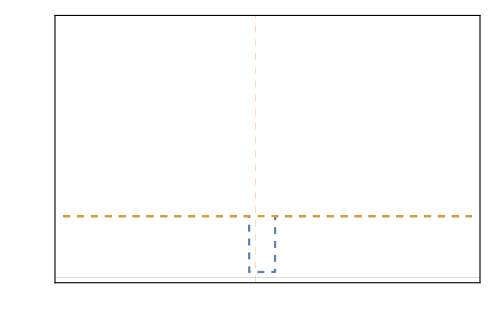

```mathematica
plotabs=LogPlot[{Abs[rhodustmin//.scalarp//.paras/.sol],Abs[rhototal//.scalarp//.paras/.sol]},{t,-1.6136*10^6,-1.613*10^6},ImageSize->500,Frame->{True,True,False,False},ImagePadding->40,PlotRange->{{-1.6136*10^6,-1.613*10^6},{10^(-12),0}},PlotLegends->{"ρ_dust","ρ_total"}];
plotarg=Plot[{-2Arg[rhodustmin//.scalarp//.paras/.sol[[1]]]/Pi+1,-2Arg[rhototal//.scalarp//.paras/.sol[[1]]]/Pi+1},{t,-1.6136*10^6,-1.613*10^6},ImageSize->500,PlotRange->{-1.2,8},Frame->{False,False,False,True},Axes->False,FrameTicks->{{False,{-1,1}},{False,False}},ImagePadding->40,PlotStyle->Dashed,GridLines->{{{t0/.tbave,Directive[Dashed,Orange,Thick]}},{-1.2}}];
plotall=Overlay[{plotabs,plotarg}]
```

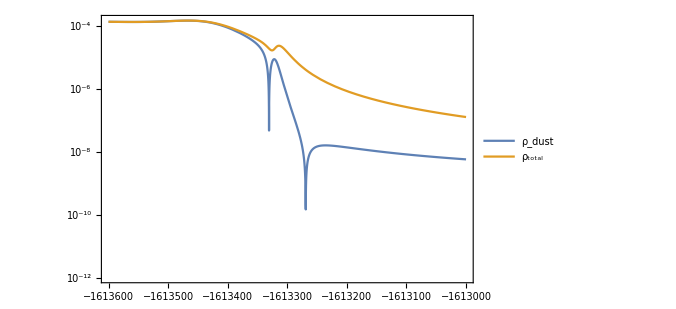
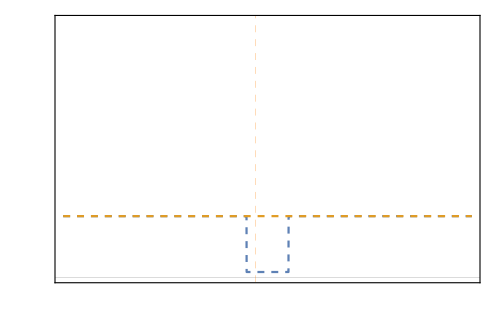

```mathematica
plotabs=LogPlot[{Abs[rhodustave//.scalarp//.paras/.solave],Abs[rhototalave//.scalarp//.paras/.solave]},{t,-1.6136*10^6,-1.613*10^6},ImageSize->500,Frame->{True,True,False,False},ImagePadding->40,PlotRange->{{-1.6136*10^6,-1.613*10^6},{10^(-12),0}},PlotLegends->{"ρ_dust","ρ_total"}];
plotarg=Plot[{-2Arg[rhodustave//.scalarp//.paras/.solave[[1]]]/Pi+1,-2Arg[rhototalave//.scalarp//.paras/.solave[[1]]]/Pi+1},{t,-1.6136*10^6,-1.613*10^6},ImageSize->500,PlotRange->{-1.2,8},Frame->{False,False,False,True},Axes->False,FrameTicks->{{False,{-1,1}},{False,False}},ImagePadding->40,PlotStyle->Dashed,GridLines->{{{t0/.tbave,Directive[Dashed,Orange,Thick]}},{-1.2}}];
plotall=Overlay[{plotabs,plotarg}]
```

## Output as Julia functions

```mathematica
newH0novnewschemefsimp=Import["newH0novnewschemefsimpccdN2.zip","newH0novnewschemefsimpccdN2.wl"];
```

```mathematica
newH0novnewschemefsimp1=Partition[(newH0novnewschemefsimp//ExpToTrig)/.Sin[x_+y_]->Cos[y] Sin[x]+Cos[x] Sin[y]/.Cos[x_+y_]->Cos[x] Cos[y]-Sin[x] Sin[y]//.Csc[x_]->Defer[1/Sin[x]]/.Cot[x_]->Defer[Cos[x]/Sin[x]],20];
```

```mathematica
sinl=DeleteDuplicates@Cases[newH0novnewschemefsimp1,Sin[xx_]->xx,-1]
```

{2 β λ b0[t],β λ b0[t],3 β λ b0[t],4 β λ b0[t],5 β λ b0[t],6 β λ b0[t],(2 kx λ)/v[t]^(1/3),(3 kx λ)/v[t]^(1/3),(kx λ)/(2 v[t]^(1/3)),1/2 β λ b0[t],(kx λ)/v[t]^(1/3),7 β λ b0[t],3/2 β λ b0[t],5/2 β λ b0[t],7/2 β λ b0[t],9/2 β λ b0[t],(4 kx λ)/v[t]^(1/3),(5 kx λ)/v[t]^(1/3),(6 kx λ)/v[t]^(1/3),(7 kx λ)/v[t]^(1/3),(3 kx λ)/(2 v[t]^(1/3)),(5 kx λ)/(2 v[t]^(1/3))}

```mathematica
cosl=DeleteDuplicates@Cases[newH0novnewschemefsimp1,Cos[xx_]->xx,-1]
```

{(kx λ)/v[t]^(1/3),(2 kx λ)/v[t]^(1/3),(3 kx λ)/v[t]^(1/3),2 β λ b0[t],3 β λ b0[t],β λ b0[t],(kx λ)/(2 v[t]^(1/3)),1/2 β λ b0[t],4 β λ b0[t],5 β λ b0[t],6 β λ b0[t],(3 kx λ)/(2 v[t]^(1/3)),(5 kx λ)/(2 v[t]^(1/3)),(4 kx λ)/v[t]^(1/3),(5 kx λ)/v[t]^(1/3),(6 kx λ)/v[t]^(1/3),(7 kx λ)/v[t]^(1/3),3/2 β λ b0[t],5/2 β λ b0[t],7/2 β λ b0[t],9/2 β λ b0[t],11/2 β λ b0[t],7 β λ b0[t]}

```mathematica
Cases[newH0novnewschemefsimp1,Exp[xx_]->xx,-1]
```

{}

```mathematica
genrulecos[rr1_]:=Module[{rr=rr1/. 1/v[t]^(1/3)->1/A[t]},pref=Level[rr,1][[1]];prefstring=If[NumberQ[pref],StringReplace[ToString[pref,InputForm],"/"->"d"],"1"];If[Length[Cases[rr,b0[t]]]>0,Cos[rr1]->ToExpression@("csb0"<>prefstring),Cos[rr1]->ToExpression@("cskl"<>prefstring)]]
genrulesin[rr1_]:=Module[{rr=rr1/. 1/v[t]^(1/3)->1/A[t]},pref=Level[rr,1][[1]];prefstring=If[NumberQ[pref],StringReplace[ToString[pref,InputForm],"/"->"d"],"1"];If[Length[Cases[rr,b0[t]]]>0,Sin[rr1]->ToExpression@("snb0"<>prefstring),Sin[rr1]->ToExpression@("snkl"<>prefstring)]]
```

```mathematica
genfuncos[rr1_]:=Module[{rr=rr1/. 1/v[t]^(1/3)->1/A[t]},pref=Level[rr,1][[1]];prefstring=If[NumberQ[pref],StringReplace[ToString[pref,InputForm],"/"->"d"],"1"];If[Length[Cases[rr,b0[t]]]>0,"csb0"<>prefstring<>"= cos("<>StringReplace[prefstring,"d"->"/"]<>"*blb0)","cskl"<>prefstring<>"= cos("<>StringReplace[prefstring,"d"->"/"]<>"*kl)"]]
```

```mathematica
genfunsin[rr1_]:=Module[{rr=rr1/. 1/v[t]^(1/3)->1/A[t]},pref=Level[rr,1][[1]];prefstring=If[NumberQ[pref],StringReplace[ToString[pref,InputForm],"/"->"d"],"1"];If[Length[Cases[rr,b0[t]]]>0,"snb0"<>prefstring<>"= sin("<>StringReplace[prefstring,"d"->"/"]<>"*blb0)","snkl"<>prefstring<>"= sin("<>StringReplace[prefstring,"d"->"/"]<>"*kl)"]]
```

```mathematica
genfun1cos[rr1_]:=Module[{rr=rr1/. 1/v[t]^(1/3)->1/A[t]},pref=Level[rr,1][[1]];prefstring=If[NumberQ[pref],StringReplace[ToString[pref,InputForm],"/"->"d"],"1"];If[Length[Cases[rr,b0[t]]]>0," cos("<>StringReplace[prefstring,"d"->"/"]<>"*blb0)"," cos("<>StringReplace[prefstring,"d"->"/"]<>"*kl)"]]
```

```mathematica
genfun1sin[rr1_]:=Module[{rr=rr1/. 1/v[t]^(1/3)->1/A[t]},pref=Level[rr,1][[1]];prefstring=If[NumberQ[pref],StringReplace[ToString[pref,InputForm],"/"->"d"],"1"];If[Length[Cases[rr,b0[t]]]>0," sin("<>StringReplace[prefstring,"d"->"/"]<>"*blb0)","sin("<>StringReplace[prefstring,"d"->"/"]<>"*kl)"]]
```

```mathematica
genheadcos[rr1_]:=Module[{rr=rr1/. 1/v[t]^(1/3)->1/A[t]},pref=Level[rr,1][[1]];prefstring=If[NumberQ[pref],StringReplace[ToString[pref,InputForm],"/"->"d"],"1"];If[Length[Cases[rr,b0[t]]]>0,"csb0"<>prefstring,"cskl"<>prefstring]]
```

```mathematica
genheadsin[rr1_]:=Module[{rr=rr1/. 1/v[t]^(1/3)->1/A[t]},pref=Level[rr,1][[1]];prefstring=If[NumberQ[pref],StringReplace[ToString[pref,InputForm],"/"->"d"],"1"];If[Length[Cases[rr,b0[t]]]>0,"snb0"<>prefstring,"snkl"<>prefstring]]
```

```mathematica
cssintostring=Join[Map[genrulecos,cosl],Map[genrulesin,sinl]];
```

```mathematica
cssheadstring=Join[Map[genheadcos,cosl],Map[genheadsin,sinl]]
```

{cskl1,cskl2,cskl3,csb02,csb03,csb01,cskl1d2,csb01d2,csb04,csb05,csb06,cskl3d2,cskl5d2,cskl4,cskl5,cskl6,cskl7,csb03d2,csb05d2,csb07d2,csb09d2,csb011d2,csb07,snb02,snb01,snb03,snb04,snb05,snb06,snkl2,snkl3,snkl1d2,snb01d2,snkl1,snb07,snb03d2,snb05d2,snb07d2,snb09d2,snkl4,snkl5,snkl6,snkl7,snkl3d2,snkl5d2}

```mathematica
cssrightstring=Join[Map[genfun1cos,cosl],Map[genfun1sin,sinl]]
```

{ cos(1*kl), cos(2*kl), cos(3*kl), cos(2*blb0), cos(3*blb0), cos(1*blb0), cos(1/2*kl), cos(1/2*blb0), cos(4*blb0), cos(5*blb0), cos(6*blb0), cos(3/2*kl), cos(5/2*kl), cos(4*kl), cos(5*kl), cos(6*kl), cos(7*kl), cos(3/2*blb0), cos(5/2*blb0), cos(7/2*blb0), cos(9/2*blb0), cos(11/2*blb0), cos(7*blb0), sin(2*blb0), sin(1*blb0), sin(3*blb0), sin(4*blb0), sin(5*blb0), sin(6*blb0),sin(2*kl),sin(3*kl),sin(1/2*kl), sin(1/2*blb0),sin(1*kl), sin(7*blb0), sin(3/2*blb0), sin(5/2*blb0), sin(7/2*blb0), sin(9/2*blb0),sin(4*kl),sin(5*kl),sin(6*kl),sin(7*kl),sin(3/2*kl),sin(5/2*kl)}

```mathematica
csextrans=Table[ToExpression@cssheadstring[[i]]->"cslist["<>ToString[i]<>"]",{i,1,Length[cssheadstring]}]
```

{cskl1→cslist[1],cskl2→cslist[2],cskl3→cslist[3],csb02→cslist[4],csb03→cslist[5],csb01→cslist[6],cskl1d2→cslist[7],csb01d2→cslist[8],csb04→cslist[9],csb05→cslist[10],csb06→cslist[11],cskl3d2→cslist[12],cskl5d2→cslist[13],cskl4→cslist[14],cskl5→cslist[15],cskl6→cslist[16],cskl7→cslist[17],csb03d2→cslist[18],csb05d2→cslist[19],csb07d2→cslist[20],csb09d2→cslist[21],csb011d2→cslist[22],csb07→cslist[23],snb02→cslist[24],snb01→cslist[25],snb03→cslist[26],snb04→cslist[27],snb05→cslist[28],snb06→cslist[29],snkl2→cslist[30],snkl3→cslist[31],snkl1d2→cslist[32],snb01d2→cslist[33],snkl1→cslist[34],snb07→cslist[35],snb03d2→cslist[36],snb05d2→cslist[37],snb07d2→cslist[38],snb09d2→cslist[39],snkl4→cslist[40],snkl5→cslist[41],snkl6→cslist[42],snkl7→cslist[43],snkl3d2→cslist[44],snkl5d2→cslist[45]}

```mathematica
cslist2=Table["\"cslist("<>ToString[i]<>")\""->"cslist["<>ToString[i]<>"]",{i,1,Length[cssheadstring]}]
```

{"cslist(1)"→cslist[1],"cslist(2)"→cslist[2],"cslist(3)"→cslist[3],"cslist(4)"→cslist[4],"cslist(5)"→cslist[5],"cslist(6)"→cslist[6],"cslist(7)"→cslist[7],"cslist(8)"→cslist[8],"cslist(9)"→cslist[9],"cslist(10)"→cslist[10],"cslist(11)"→cslist[11],"cslist(12)"→cslist[12],"cslist(13)"→cslist[13],"cslist(14)"→cslist[14],"cslist(15)"→cslist[15],"cslist(16)"→cslist[16],"cslist(17)"→cslist[17],"cslist(18)"→cslist[18],"cslist(19)"→cslist[19],"cslist(20)"→cslist[20],"cslist(21)"→cslist[21],"cslist(22)"→cslist[22],"cslist(23)"→cslist[23],"cslist(24)"→cslist[24],"cslist(25)"→cslist[25],"cslist(26)"→cslist[26],"cslist(27)"→cslist[27],"cslist(28)"→cslist[28],"cslist(29)"→cslist[29],"cslist(30)"→cslist[30],"cslist(31)"→cslist[31],"cslist(32)"→cslist[32],"cslist(33)"→cslist[33],"cslist(34)"→cslist[34],"cslist(35)"→cslist[35],"cslist(36)"→cslist[36],"cslist(37)"→cslist[37],"cslist(38)"→cslist[38],"cslist(39)"→cslist[39],"cslist(40)"→cslist[40],"cslist(41)"→cslist[41],"cslist(42)"→cslist[42],"cslist(43)"→cslist[43],"cslist(44)"→cslist[44],"cslist(45)"→cslist[45]}

```mathematica
cslisttrans=Table[cssheadstring[[i]]->"cslist["<>ToString[i]<>"]",{i,1,Length[cssheadstring]}]
```

{cskl1→cslist[1],cskl2→cslist[2],cskl3→cslist[3],csb02→cslist[4],csb03→cslist[5],csb01→cslist[6],cskl1d2→cslist[7],csb01d2→cslist[8],csb04→cslist[9],csb05→cslist[10],csb06→cslist[11],cskl3d2→cslist[12],cskl5d2→cslist[13],cskl4→cslist[14],cskl5→cslist[15],cskl6→cslist[16],cskl7→cslist[17],csb03d2→cslist[18],csb05d2→cslist[19],csb07d2→cslist[20],csb09d2→cslist[21],csb011d2→cslist[22],csb07→cslist[23],snb02→cslist[24],snb01→cslist[25],snb03→cslist[26],snb04→cslist[27],snb05→cslist[28],snb06→cslist[29],snkl2→cslist[30],snkl3→cslist[31],snkl1d2→cslist[32],snb01d2→cslist[33],snkl1→cslist[34],snb07→cslist[35],snb03d2→cslist[36],snb05d2→cslist[37],snb07d2→cslist[38],snb09d2→cslist[39],snkl4→cslist[40],snkl5→cslist[41],snkl6→cslist[42],snkl7→cslist[43],snkl3d2→cslist[44],snkl5d2→cslist[45]}

```mathematica
csrightlist=Table["cslist["<>ToString[i]<>"] = "<>cssrightstring[[i]],{i,1,Length[cssheadstring]}]
```

{cslist[1] =  cos(1*kl),cslist[2] =  cos(2*kl),cslist[3] =  cos(3*kl),cslist[4] =  cos(2*blb0),cslist[5] =  cos(3*blb0),cslist[6] =  cos(1*blb0),cslist[7] =  cos(1/2*kl),cslist[8] =  cos(1/2*blb0),cslist[9] =  cos(4*blb0),cslist[10] =  cos(5*blb0),cslist[11] =  cos(6*blb0),cslist[12] =  cos(3/2*kl),cslist[13] =  cos(5/2*kl),cslist[14] =  cos(4*kl),cslist[15] =  cos(5*kl),cslist[16] =  cos(6*kl),cslist[17] =  cos(7*kl),cslist[18] =  cos(3/2*blb0),cslist[19] =  cos(5/2*blb0),cslist[20] =  cos(7/2*blb0),cslist[21] =  cos(9/2*blb0),cslist[22] =  cos(11/2*blb0),cslist[23] =  cos(7*blb0),cslist[24] =  sin(2*blb0),cslist[25] =  sin(1*blb0),cslist[26] =  sin(3*blb0),cslist[27] =  sin(4*blb0),cslist[28] =  sin(5*blb0),cslist[29] =  sin(6*blb0),cslist[30] = sin(2*kl),cslist[31] = sin(3*kl),cslist[32] = sin(1/2*kl),cslist[33] =  sin(1/2*blb0),cslist[34] = sin(1*kl),cslist[35] =  sin(7*blb0),cslist[36] =  sin(3/2*blb0),cslist[37] =  sin(5/2*blb0),cslist[38] =  sin(7/2*blb0),cslist[39] =  sin(9/2*blb0),cslist[40] = sin(4*kl),cslist[41] = sin(5*kl),cslist[42] = sin(6*kl),cslist[43] = sin(7*kl),cslist[44] = sin(3/2*kl),cslist[45] = sin(5/2*kl)}

```mathematica
Vlisttrans=Table[{"V1t","V2t","dV1t","dV2t","ddV1t","ddV2t"}[[i]]->"VVt["<>ToString[i]<>"]",{i,1,6}]
```

{V1t→VVt[1],V2t→VVt[2],dV1t→VVt[3],dV2t→VVt[4],ddV1t→VVt[5],ddV2t→VVt[6]}

```mathematica
varlisttrans=Table[{"v","b0","Phi","gPi"}[[i]]->"bv_l["<>ToString[i]<>"]",{i,1,4}]
```

{v→bv_l[1],b0→bv_l[2],Phi→bv_l[3],gPi→bv_l[4]}

```mathematica
dvarlisttrans=Table[{"dv","db0","dPhi","dgPi"}[[i]]->"dbv_l["<>ToString[i]<>"]",{i,1,4}]
```

{dv→dbv_l[1],db0→dbv_l[2],dPhi→dbv_l[3],dgPi→dbv_l[4]}

```mathematica
parastrans=Table[Map[ToString,{lambda, beta, alpha, kappa, Clambda, ms,k0 }][[i]]->"paras["<>ToString[i]<>"]",{i,1,7}]
```

{lambda→paras[1],beta→paras[2],alpha→paras[3],kappa→paras[4],Clambda→paras[5],ms→paras[6],k0→paras[7]}

```mathematica
newH0novnewschemefsimps=Simplify[newH0novnewschemefsimp1/.cssintostring];
```

```mathematica
rsepacial={"λϕ"->"lamphi","λ"->"lambda","β"->"beta","Π"->"gPi","Φ"->"Phi","κ"->"kappa","α"->"alpha","ρ"->"rho","Λ"->"Clambda"};
```

```mathematica
Hstring=Map[StringReplace[ToString[#/.lo->1/.Defer[x_]->x/.E^(x$111___)->exp[x$111]/.(x$111___)^n_->pow[x$111,n]/.b0[t]->b0/.v[t]->v/.v'[t]->dv/.b0'[t]->db0/.v''[t]->ddv/.b0''[t]->ddb0/.Φ[t]->Φ/.Π[t]->Π/.Π'[t]->dΠ/.Πrho[t]->Πrho/.Φ'[t]->dΦ/.Πrho'[t]->dΠrho/.V1[x$111_]->V1t/.V2[x$111_]->V2t/.V1'[x$111_]->dV1t/.V2'[x$111_]->dV2t/.V1''[x$111_]->ddV1t/.V2''[x$111_]->ddV2t/.Cos[x$111___]->cos[x$111]/.Cot[x$111___]->cot[x$111]/.Sin[x$111___]->sin[x$111]/.Csc[x$111___]->csc[x$111]/.ρdust[t]->ρdust/.kx->k/.ⅈ->im/.I->im/. 0->(0.)//InputForm],Join[{"["->"(","]"->")","I"->"im","0."->"0."},rsepacial]]&, Flatten[Transpose[newH0novnewschemefsimps]]];
```

```mathematica
Hstringt=StringReplace[Hstring=Map[StringReplace[ToString[#/.lo->1/.Defer[x_]->x/.E^(x$111___)->exp[x$111]/.(x$111___)^n_->pow[x$111,n]/.b0[t]->b0/.v[t]->v/.v'[t]->dv/.b0'[t]->db0/.v''[t]->ddv/.b0''[t]->ddb0/.Φ[t]->Φ/.Π[t]->Π/.Π'[t]->dΠ/.Πrho[t]->Πrho/.Φ'[t]->dΦ/.Πrho'[t]->dΠrho/.V1[x$111_]->V1t/.V2[x$111_]->V2t/.V1'[x$111_]->dV1t/.V2'[x$111_]->dV2t/.V1''[x$111_]->ddV1t/.V2''[x$111_]->ddV2t/.Cos[x$111___]->cos[x$111]/.Cot[x$111___]->cot[x$111]/.Sin[x$111___]->sin[x$111]/.Csc[x$111___]->csc[x$111]/.ρdust[t]->ρdust/.kx->k/.ⅈ->im/.I->im/. 0->(0.)/.csextrans//InputForm],Join[{"["->"(","]"->")","I"->"im","0."->"0."},rsepacial]]&, Flatten[Transpose[newH0novnewschemefsimps]]],Join[cslist2,Vlisttrans,varlisttrans,dvarlisttrans,parastrans]];
```

```mathematica
file=OpenWrite["HHijfun_st.jl"];
WriteString[file,"function calcslist(vars,paras,cslist) \n "];
WriteString[file,"kl= paras[7]*paras[1]/vars[1]^(1/3); 
blb0=paras[2]*paras[1]*vars[2]; \n"];
Do[WriteString[file,csrightlist[[i]]<>"; \n"],{i,1,Length[csrightlist]}];
WriteString[file,"return nothing; \n end \n"];
WriteString[file,"function HHijfun(index,vars,dvars,VVt,rhodust,cslist,paras) \n (ii,jj)=index; \n"];
WriteString[file,"return getfield(Main,Symbol(\"HHijfun\",(ii-1)*20+jj))(bv_l,dbv_l,rhodust,cslist,VVt,paras); \n"];
WriteString[file," end \n"];
Do[WriteString[file,"function HHijfun"<>ToString[j]<>"(bv_l,dbv_l,rhodust,cslist,VVt,paras) \n"];
If[StringLength[Hstringt[[j]]]=!=2,WriteString[file, "\n"]];
WriteString[file,"    "<>Hstringt[[j]]<>"  \n"];
WriteString[file," end \n"];,{j,1,Length[Hstringt]}];
Close["HHijfun_st.jl"];
```

#### Constraint fun

```mathematica
constraintmatrix=D[{D[Nshiftd,ϵ],D[Hphys/(μ^3),ϵ],aa^2clo/ϵ1/(μ^3)}/.transrule1//.transrulebv/.ϵ->1/.va[i_][t]->va[i]//Normal//Flatten,{Table[va[i],{i,1,20}]}]//Expand//Simplify;
```

```mathematica
constraintmatrixc=Series[constraintmatrix,{λ,0,0}]//Normal//FullSimplify;
```

```mathematica
constraintstring=Table[StringReplace[ToString[constraintmatrix[[i,j]]/.lo->1/.E^(x$111___)->exp[x$111]/.(x$111___)^n_->pow[x$111,n]/.b0[t]->b0/.v[t]->v/.v'[t]->dv/.b0'[t]->db0/.v''[t]->ddv/.b0''[t]->ddb0/.Φ[t]->Φ/.Π[t]->Π/.Φ'[t]->dΦ/.Π'[t]->dΠ/.V1[x$111_]->V1t/.V2[x$111_]->V2t/.V1'[x$111_]->dV1t/.V2'[x$111_]->dV2t/.V1''[x$111_]->ddV1t/.V2''[x$111_]->ddV2t/.Cos[x$111___]->cos[x$111]/.Cot[x$111___]->cot[x$111]/.Sin[x$111___]->sin[x$111]/.Csc[x$111___]->csc[x$111]/.ρdust[t]->ρdust/.kx->k/.ⅈ->im/.I->im//InputForm],Join[{"["->"(","]"->")","I"->"im"},rsepacial]],{i,1,7},{j,1,20}];
file=OpenWrite["invariant_function_matrix_n.jl"];
WriteString[file,"function constraint_fun(tmp,var_back,paras) 
  v,b0,Phi,gPi=var_back; 
 lambda, beta, alpha, kappa, Clambda, ms , k=paras; \n
V1t=V1(Phi,paras);
V2t=V2(Phi,paras);
dV1t=dV1(Phi,paras);
dV2t=dV2(Phi,paras);
ddV1t=ddV1(Phi,paras);
ddV2t=ddV2(Phi,paras);
 \n"];
Table[WriteString[file,"    tmp["<>ToString[i]<>","<>ToString[j]<>"] = "<>constraintstring[[i,j]]<>" ;  \n"],{i,1,7},{j,1,20}];
WriteString[file," end \n"]
Close["invariant_function_matrix_n.jl"];
```

```mathematica
constraintcstring=Table[StringReplace[ToString[constraintmatrixc[[i,j]]/.lo->1/.λϕ->1/.E^(x$111___)->exp[x$111]/.(x$111___)^n_->pow[x$111,n]/.b0[t]->b0/.v[t]->v/.v'[t]->dv/.b0'[t]->db0/.v''[t]->ddv/.b0''[t]->ddb0/.Φ[t]->Φ/.Π[t]->Π/.Φ'[t]->dΦ/.Π'[t]->dΠ/.V1[x$111_]->V1t/.V2[x$111_]->V2t/.V1'[x$111_]->dV1t/.V2'[x$111_]->dV2t/.V1''[x$111_]->ddV1t/.V2''[x$111_]->ddV2t/.Cos[x$111___]->cos[x$111]/.Cot[x$111___]->cot[x$111]/.Sin[x$111___]->sin[x$111]/.Csc[x$111___]->csc[x$111]/.ρdust[t]->ρdust/.kx->k/.ⅈ->im/.I->im//InputForm],Join[{"["->"(","]"->")","I"->"im"},rsepacial]],{i,1,7},{j,1,20}];
file=OpenWrite["invariant_functionc_matrix_n.jl"];
WriteString[file,"function constraintc_fun(tmp,var_back,paras) 
  v,b0,Phi,gPi=var_back; 
 lambda, beta, alpha, kappa, Clambda, ms , k=paras;  \n
V1t=V1(Phi,paras);
V2t=V2(Phi,paras);
dV1t=dV1(Phi,paras);
dV2t=dV2(Phi,paras);
ddV1t=ddV1(Phi,paras);
ddV2t=ddV2(Phi,paras);
"];
Table[WriteString[file,"    tmp["<>ToString[i]<>","<>ToString[j]<>"] = "<>constraintcstring[[i,j]]<>" ;  \n"],{i,1,7},{j,1,20}];
WriteString[file," end \n"]
Close["invariant_functionc_matrix_n.jl"];
```